## Definitions.08.08.08.08.08.08.08.08.08.08.08.08.08

```mathematica
G0=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
G1=({{0, 0, 0, 1}, {0, 0, 1, 0}, {0, -1, 0, 0}, {-1, 0, 0, 0}});
G2=({{0, 0, 0, -I}, {0, 0, I, 0}, {0, I, 0, 0}, {-I, 0, 0, 0}});
G3=({{0, 0, 1, 0}, {0, 0, 0, -1}, {-1, 0, 0, 0}, {0, 1, 0, 0}});

G5=({{0, 0, 1, 0}, {0, 0, 0, 1}, {1, 0, 0, 0}, {0, 1, 0, 0}});
```

```mathematica
$Assumptions={e∈Reals ,p0∈Reals ,p1∈Reals ,p2∈Reals ,p3∈Reals,v0∈Reals,z∈Reals,L∈Reals,e>0,m>0,v0>0,L>0,pz>0, pz∈Reals, py∈Reals, e>m, e-v0>m, e>v0+m, hx>0,hx∈Reals}
```

## Dirac’s Eq

```mathematica
etaD = (G0+I G5)/Sqrt[2];
eta = etaD;
```

```mathematica
Pz =Eigenvectors[ G0  e+  m  I G5];
```

```mathematica
PzA = %
```

{{0,(ⅈ (-e+√(e^2-m^2)))/m,0,1},{(ⅈ (-e+√(e^2-m^2)))/m,0,1,0},{0,-(ⅈ (e+√(e^2-m^2)))/m,0,1},{-(ⅈ (e+√(e^2-m^2)))/m,0,1,0}}

```mathematica
PzC = PzA/. { Sqrt[e^2 - m^2]->pz}
```

{{0,(ⅈ (-e+pz))/m,0,1},{(ⅈ (-e+pz))/m,0,1,0},{0,-(ⅈ (e+pz))/m,0,1},{-(ⅈ (e+pz))/m,0,1,0}}

```mathematica
P={{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}};

PzD =PzC.P
```

{{1,0,(ⅈ (-e+pz))/m,0},{0,1,0,(ⅈ (-e+pz))/m},{1,0,-(ⅈ (e+pz))/m,0},{0,1,0,-(ⅈ (e+pz))/m}}

```mathematica
col[v_]:=List/@v;

u1=col[PzD[[3]]];
u2=col[PzD[[4]]];

u3=col[PzD[[1]]];
u4=col[PzD[[2]]];
```

```mathematica
u1//MatrixForm
```

(1
0
-(ⅈ (e+pz))/m
0)

```mathematica
ConjugateTranspose[u1].u2//FullSimplify
```

{{0}}

```mathematica
Fu1[ee_,ppz_]:=u1/. {e->ee, pz->ppz}
Fu2[ee_,ppz_]:=u2/. {e->ee, pz->ppz}
Fu3[ee_,ppz_]:=u3/. {e->ee, pz->ppz}
Fu4[ee_,ppz_]:=u4/. {e->ee, pz->ppz}
```

```mathematica
Fu1[e,p1]
```

{{1},{0},{-(ⅈ (e+p1))/m},{0}}

```mathematica
psiIN = a Fu1[e,p1];
psiR = b Fu1[e,-p1] + bp Fu2[e,-p1];
psiT = c  Fu1[e-v0,p2]+ cp Fu2[e-v0,p2];
```

```mathematica
Xm =G0
```

{{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}}

```mathematica
jin= ConjugateTranspose[psiIN].Xm.psiIN//FullSimplify
```

{{-(a (e-m+p1) (e+m+p1) Conjugate[a])/m^2}}

```mathematica
jR= ConjugateTranspose[psiR].Xm.psiR//FullSimplify
```

{{((e+m-p1) (-e+m+p1) (Abs[b]^2+Abs[bp]^2))/m^2}}

```mathematica
jT = ConjugateTranspose[psiT].Xm.psiT//FullSimplify
```

{{((e+m+p2-v0) (-e+m-p2+v0) (Abs[c]^2+Abs[cp]^2))/m^2}}

```mathematica
jR/jin/.{p1-> Sqrt[e^2-m^2],p2-> Sqrt[(e-v0)^2-m^2]}//FullSimplify
```

{{(m^2 (Abs[b]^2+Abs[bp]^2))/((m^2-2 e (e+√((e-m) (e+m)))) Abs[a]^2)}}

```mathematica
jT/jin/.{p1-> Sqrt[e^2-m^2],p2-> Sqrt[(e-v0)^2-m^2]}//FullSimplify
```

{{((e-m-v0+√(e^2-m^2-2 e v0+v0^2)) (e+m-v0+√(e^2-m^2-2 e v0+v0^2)) (Abs[c]^2+Abs[cp]^2))/(2 a (-m^2+e (e+√((e-m) (e+m)))) Conjugate[a])}}

```mathematica
nt =((e-m-v0+√(e^2-m^2-2 e v0+v0^2)) (e+m-v0+√(e^2-m^2-2 e v0+v0^2)))/(2  (-m^2+e (e+√(e^2-m^2))));(*G3*)
nr = m^2/(m^2-2 e (e+√(e^2-m^2)));
```

```mathematica
sol1 = Solve[a Fu1[e,p1]+b Fu1[e,-p1] + bp Fu2[e,-p1]==c  Fu1[e-v0,p2]+ cp Fu2[e-v0,p2],{a,b,c,bp,cp}]//FullSimplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a→(c (p1+p2-v0))/(2 p1),b→(c (p1-p2+v0))/(2 p1),bp→0,cp→0}}

```mathematica
sol2 = sol1/.{p1-> Sqrt[e^2-m^2],p2-> Sqrt[(e-v0)^2-m^2]}//FullSimplify
```

{{a→(c (√((e-m) (e+m))+√(-m^2+(e-v0)^2)-v0))/(2 √((e-m) (e+m))),b→(c (√((e-m) (e+m))-√(-m^2+(e-v0)^2)+v0))/(2 √((e-m) (e+m))),bp→0,cp→0}}

```mathematica
Tr1=(c/.sol2)/(a/.sol2)//FullSimplify
```

{(2 √((e-m) (e+m)))/(√((e-m) (e+m))+√(-m^2+(e-v0)^2)-v0)}

```mathematica
Tr2=(cp/.sol2)/(a/.sol2)//FullSimplify
```

{0}

```mathematica
Rf1=(b/.sol2)/(a/.sol2)//FullSimplify
```

{(√((e-m) (e+m))-√(-m^2+(e-v0)^2)+v0)/(√((e-m) (e+m))+√(-m^2+(e-v0)^2)-v0)}

```mathematica
Rf2=(bp/.sol2)/(a/.sol2)//FullSimplify
```

{0}

```mathematica
Ttotal = nt(modsq[ Tr1[[1]] ]+modsq[ Tr2[[1]] ] )//FullSimplify
```

(2 (e-m) (e+m) (e-m-v0+√(e^2-m^2-2 e v0+v0^2)) (e+m-v0+√(e^2-m^2-2 e v0+v0^2)))/((-m^2+e (e+√((e-m) (e+m)))) (√((e-m) (e+m))-v0+√(e^2-m^2-2 e v0+v0^2))^2)

```mathematica
Limit[Ttotal,v0->∞]//FullSimplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

2-(2 e (e+√((e-m) (e+m))))/m^2

```mathematica
Limit[Ttotal,v0->0]//FullSimplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1

```mathematica
Rtot = nr(modsq[ Rf1[[1]] ]+modsq[ Rf2[[1]] ] )//FullSimplify
```

(m^2 (√((e-m) (e+m))+v0-√(e^2-m^2-2 e v0+v0^2))^2)/((m^2-2 e (e+√((e-m) (e+m)))) (√((e-m) (e+m))-v0+√(e^2-m^2-2 e v0+v0^2))^2)

```mathematica
Limit[Rtot,v0->∞]//FullSimplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

-(e+√((e-m) (e+m)))^2/m^2

```mathematica
Limit[Rtot,v0->0]//FullSimplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

0

```mathematica
TotP [ee_,v00_,mm_]:=nt(modsq[  Tr1[[1]] ]+modsq[ Tr2[[1]] ] )+nr(  modsq[  Rf1[[1]] ]+modsq[ Rf2[[1]] ])/. {e->ee, v0->v00, m->mm}
```

```mathematica
Plot3D[TotP [e,v0,1],{e,2,1000},{v0,1,100}]
```

-Graphics3D-

```mathematica
me=9.1*10^-31;
cv=3*10^8;
ev=me*cv^2/(1.6*10^-19);
mev=me*cv^2/(1.6*10^-19);
jev=(1.6*10^-19);
vstep=10^6;
```

```mathematica
Tup[ee_,v00_,mm_]:= Abs[nt modsq[ Tr1[[1]] ]]/. {e->ee, v0->v00, m->mm}
Tdn[ee_,v00_,mm_]:= Abs[nt modsq[Tr2[[1]] ]]/. {e->ee, v0->v00, m->mm}
Rup[ee_,v00_,mm_]:=Abs[ nr modsq[ Rf1[[1]] ]]/. {e->ee, v0->v00, m->mm}
Rdn[ee_,v00_,mm_]:= Abs[nr modsq[ Rf2[[1]] ]]/. {e->ee, v0->v00, m->mm}
```

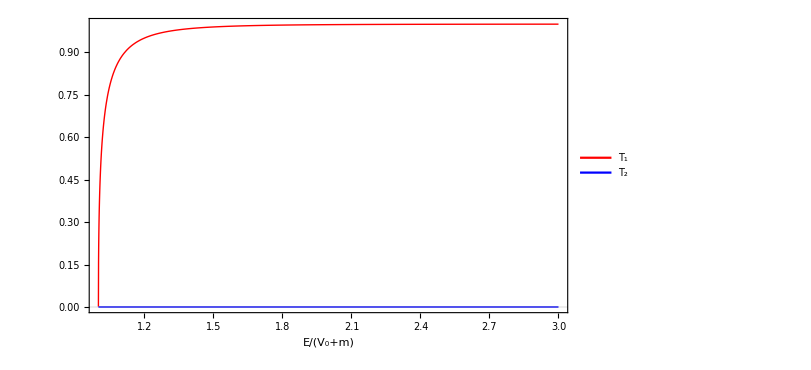

```mathematica
Plot[{Tup[x*(vstep+mev),(vstep+1/2 mev),1/2 mev],Tdn[x*(vstep+mev),(vstep+1/2mev),1/2mev]},{x,1,3},PlotStyle->{{Red,Thick},{Blue,Thick}},Frame->True,FrameLabel->{Style["E/(V₀+m)",18,Italic],None},PlotLegends->Placed[{Style["T₁",18,Italic],Style["T₂",18,Italic]},{0.8,0.2}],ImageSize->{600,600},FrameTicksStyle->Directive[Black,14],PlotRange->All,PlotTheme->"Scientific"]
```

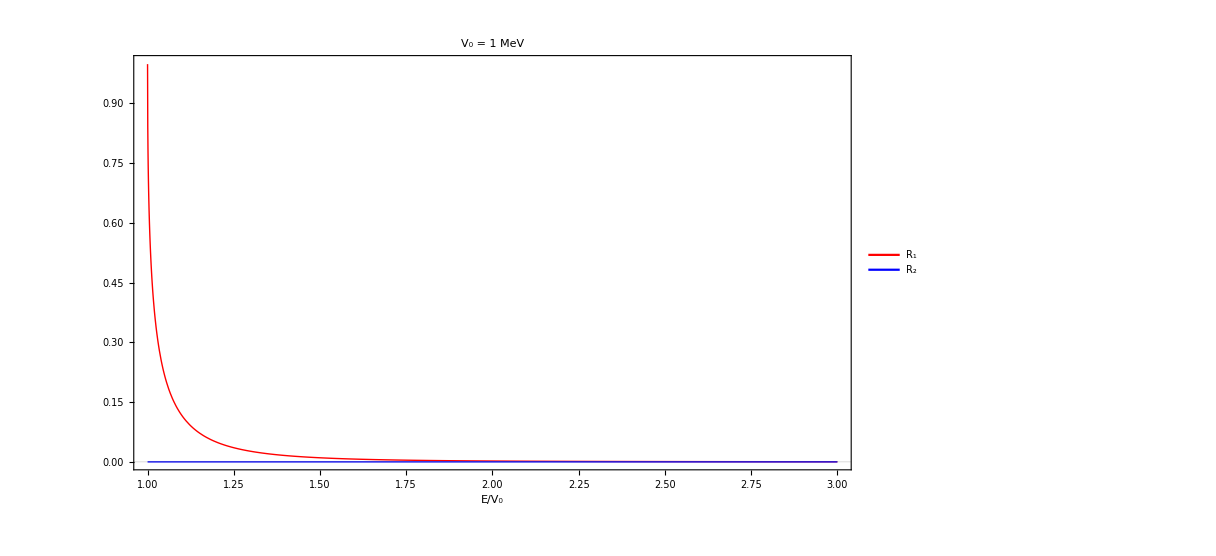

```mathematica
Plot[{Rup[x*(vstep+mev),(vstep+1/2mev),1/2mev],Rdn[x*(vstep+mev),(vstep+1/2mev),1/2mev]},{x,1,3},PlotStyle->{{Red,Thick},{Blue,Thick}},PlotRange->{{1,3},{0,1}},Frame->True,FrameLabel->{Style["E/V₀",18,Italic],None},PlotLegends->Placed[{Style["R₁",18,Italic],Style["R₂",18,Italic]},{0.75,0.3}],ImageSize->{900,600},FrameTicksStyle->Directive[Black,14],FrameStyle->Directive[Black,14],(*✅ replaces FrameLabelStyle*)PlotTheme->"Scientific",PlotLabel->Style["V₀ = 1 MeV",18,Italic]]
```

```mathematica
Rup[(vstep+mev),(vstep+1/2mev),1/2mev]
```

-1.

## Ajaib’s Representation

```mathematica
etaA = -I/Sqrt[2](G0.G1.G5+ G2);
eta = etaA;
```

```mathematica
x1 = (eta + ConjugateTranspose[eta])/Sqrt[2];
x2 =  (eta - ConjugateTranspose[eta])/Sqrt[2];
```

```mathematica
Pz =Eigenvectors[ x1  e+  m  x2];
```

```mathematica
PzA = %
```

{{(√(e^2-m^2))/e,(ⅈ m)/e,0,1},{-(ⅈ m)/e,-(√(e^2-m^2))/e,1,0},{-(√(e^2-m^2))/e,(ⅈ m)/e,0,1},{-(ⅈ m)/e,(√(e^2-m^2))/e,1,0}}

```mathematica
PzC = PzA/.  { Sqrt[e^2 - m^2]->pz}
```

{{pz/e,(ⅈ m)/e,0,1},{-(ⅈ m)/e,-pz/e,1,0},{-pz/e,(ⅈ m)/e,0,1},{-(ⅈ m)/e,pz/e,1,0}}

```mathematica
P={{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}};

PzD =PzC.P
```

{{1,0,(ⅈ m)/e,pz/e},{0,1,-pz/e,-(ⅈ m)/e},{1,0,(ⅈ m)/e,-pz/e},{0,1,pz/e,-(ⅈ m)/e}}

```mathematica
col[v_]:=List/@v;

u1=col[PzD[[3]]];
u2=col[PzD[[4]]];

u3=col[PzD[[1]]];
u4=col[PzD[[2]]];
```

```mathematica
u1//MatrixForm
```

(1
0
(ⅈ m)/e
-pz/e)

```mathematica
ConjugateTranspose[u1].u2//FullSimplify
```

{{0}}

```mathematica
Fu1[ee_,ppz_]:=u1/. {e->ee, pz->ppz}
Fu2[ee_,ppz_]:=u2/. {e->ee, pz->ppz}
Fu3[ee_,ppz_]:=u3/. {e->ee, pz->ppz}
Fu4[ee_,ppz_]:=u4/. {e->ee, pz->ppz}
```

```mathematica
Fu1[e,p1]
```

{{1},{0},{(ⅈ m)/e},{-p1/e}}

```mathematica
psiIN = a Fu1[e,p1];
psiR = b Fu1[e,-p1] + bp Fu2[e,-p1];
psiT = c  Fu1[e-v0,p2]+ cp Fu2[e-v0,p2];
```

```mathematica
Xm =eta + ConjugateTranspose[eta]
```

{{0,0,0,-√2},{0,0,√2,0},{0,√2,0,0},{-√2,0,0,0}}

```mathematica
jin= ConjugateTranspose[psiIN].Xm.psiIN//FullSimplify
```

{{(2 √2 a p1 Conjugate[a])/e}}

```mathematica
jR= ConjugateTranspose[psiR].Xm.psiR//FullSimplify
```

{{-(2 √2 p1 (Abs[b]^2+Abs[bp]^2))/e}}

```mathematica
jT = ConjugateTranspose[psiT].Xm.psiT//FullSimplify
```

{{(2 √2 p2 (Abs[c]^2+Abs[cp]^2))/(e-v0)}}

```mathematica
jR/jin/.{p1-> Sqrt[e^2-m^2],p2-> Sqrt[(e-v0)^2-m^2]}//FullSimplify
```

{{-(Abs[b]^2+Abs[bp]^2)/Abs[a]^2}}

```mathematica
jT/jin/.{p1-> Sqrt[e^2-m^2],p2-> Sqrt[(e-v0)^2-m^2]}//FullSimplify
```

{{(e √((e^2-m^2-2 e v0+v0^2)/(e^2-m^2)) (Abs[c]^2+Abs[cp]^2))/((e-v0) Abs[a]^2)}}

```mathematica
nt =(e √((e^2-m^2-2 e v0+v0^2)/(e^2-m^2)))/(e-v0);(*G3*)
nr = 1;
```

```mathematica
sol1 = Solve[a Fu1[e,p1]+b Fu1[e,-p1] + bp Fu2[e,-p1]==c  Fu1[e-v0,p2]+ cp Fu2[e-v0,p2],{a,b,c,bp,cp}]//FullSimplify
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a→-(ⅈ bp (e^2 (p1+p2)^2-2 e p1 (p1+p2) v0+(m^2+p1^2) v0^2))/(2 m p1 v0 (-e+v0)),b→(ⅈ bp (e^2 (-p1^2+p2^2)+2 e p1^2 v0+(m-p1) (m+p1) v0^2))/(2 m p1 v0 (-e+v0)),c→(ⅈ bp (e (p1+p2)-p1 v0))/(m v0),cp→bp}}

```mathematica
sol2 = sol1/.{p1-> Sqrt[e^2-m^2],p2-> Sqrt[(e-v0)^2-m^2]}//FullSimplify
```

{{a→(ⅈ bp e (e^2-m^2+√((e-m) (e+m) (e-m-v0) (e+m-v0))-e v0))/(m √((e-m) (e+m)) v0),b→(ⅈ bp m)/(√((e-m) (e+m))),c→(ⅈ bp (e (√((e-m) (e+m))+√(-m^2+(e-v0)^2))-√((e-m) (e+m)) v0))/(m v0),cp→bp}}

```mathematica
Tr1=(c/.sol2)/(a/.sol2)//FullSimplify
```

{-(-e^2+m^2+√((e-m) (e+m) (e-m-v0) (e+m-v0)))/(e v0)}

```mathematica
Tr2=(cp/.sol2)/(a/.sol2)//FullSimplify
```

{-(ⅈ m √((e-m) (e+m)) v0)/(e (e^2-m^2+√((e-m) (e+m) (e-m-v0) (e+m-v0))-e v0))}

```mathematica
Rf1=(b/.sol2)/(a/.sol2)//FullSimplify
```

{(m^2 v0)/(e (e^2-m^2+√((e-m) (e+m) (e-m-v0) (e+m-v0))-e v0))}

```mathematica
Rf2=(bp/.sol2)/(a/.sol2)//FullSimplify
```

{-(ⅈ m √((e-m) (e+m)) v0)/(e (e^2-m^2+√((e-m) (e+m) (e-m-v0) (e+m-v0))-e v0))}

```mathematica
Ttotal = nt(modsq[ Tr1[[1]] ]+modsq[ Tr2[[1]] ] )//FullSimplify
```

(2 √((e-m) (e+m) (e-m-v0) (e+m-v0)))/(e^2-m^2+√((e-m) (e+m) (e-m-v0) (e+m-v0))-e v0)

```mathematica
Limit[Ttotal,v0->∞]//FullSimplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

2-(2 e (e+√(e^2-m^2)))/m^2

```mathematica
Limit[Ttotal,v0->0]//FullSimplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1

```mathematica
Rtot = nr(modsq[ Rf1[[1]] ]+modsq[ Rf2[[1]] ] )//FullSimplify
```

(m^2 v0^2)/((e^2-m^2+√((e-m) (e+m) (e-m-v0) (e+m-v0))-e v0)^2)

```mathematica
Limit[Rtot,v0->∞]//FullSimplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

m^2/((e-√(e^2-m^2))^2)

```mathematica
Limit[Rtot,v0->0]//FullSimplify
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

0

```mathematica
TotP [ee_,v00_,mm_]:=nt(modsq[  Tr1[[1]] ]+modsq[ Tr2[[1]] ] )+nr(  modsq[  Rf1[[1]] ]+modsq[ Rf2[[1]] ])/. {e->ee, v0->v00, m->mm}
```

```mathematica
Plot3D[TotP [e,v0,1],{e,2,1000},{v0,1,100}]
```

-Graphics3D-

```mathematica
me=9.1*10^-31;
cv=3*10^8;
ev=me*cv^2/(1.6*10^-19);
mev=me*cv^2/(1.6*10^-19);
jev=(1.6*10^-19);
vstep=10^6;
```

```mathematica
Tup[ee_,v00_,mm_]:= Abs[nt modsq[ Tr1[[1]] ]]/. {e->ee, v0->v00, m->mm}
Tdn[ee_,v00_,mm_]:= Abs[nt modsq[Tr2[[1]] ]]/. {e->ee, v0->v00, m->mm}
Rup[ee_,v00_,mm_]:=Abs[ nr modsq[ Rf1[[1]] ]]/. {e->ee, v0->v00, m->mm}
Rdn[ee_,v00_,mm_]:= Abs[nr modsq[ Rf2[[1]] ]]/. {e->ee, v0->v00, m->mm}
```

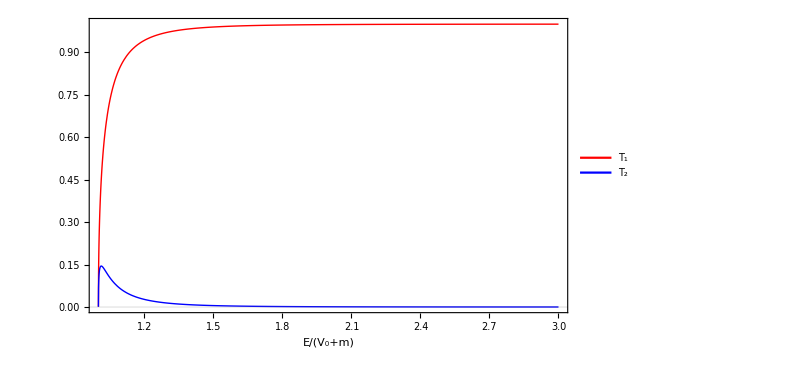

```mathematica
Plot[{Tup[x*(vstep+mev),(vstep+1/2 mev),1/2 mev],Tdn[x*(vstep+mev),(vstep+1/2mev),1/2mev]},{x,1,3},PlotStyle->{{Red,Thick},{Blue,Thick}},Frame->True,FrameLabel->{Style["E/(V₀+m)",18,Italic],None},PlotLegends->Placed[{Style["T₁",18,Italic],Style["T₂",18,Italic]},{0.8,0.2}],ImageSize->{600,600},FrameTicksStyle->Directive[Black,14],PlotRange->All,PlotTheme->"Scientific"]
```

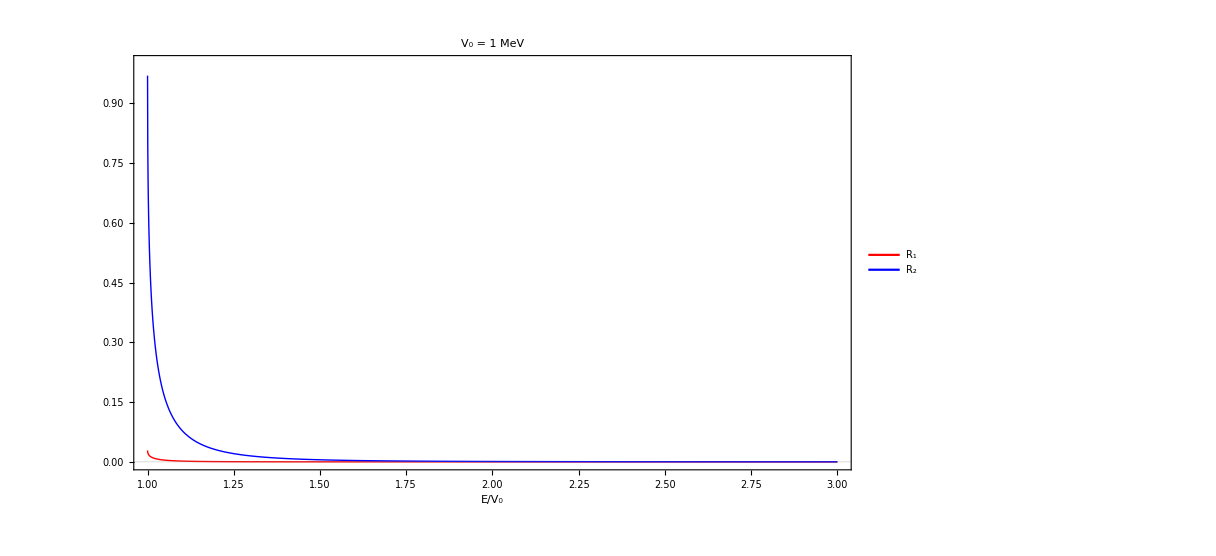

```mathematica
Plot[{Rup[x*(vstep+mev),(vstep+1/2mev),1/2mev],Rdn[x*(vstep+mev),(vstep+1/2mev),1/2mev]},{x,1,3},PlotStyle->{{Red,Thick},{Blue,Thick}},PlotRange->{{1,3},{0,1}},Frame->True,FrameLabel->{Style["E/V₀",18,Italic],None},PlotLegends->Placed[{Style["R₁",18,Italic],Style["R₂",18,Italic]},{0.75,0.3}],ImageSize->{900,600},FrameTicksStyle->Directive[Black,14],FrameStyle->Directive[Black,14],(*✅ replaces FrameLabelStyle*)PlotTheme->"Scientific",PlotLabel->Style["V₀ = 1 MeV",18,Italic]]
```